```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals;
```

system parameter:
A (int) : total number of particles
F (int) : number of fragments
Z (int array) : number of particles in fragments
d (int) : number of spatial dimensions (ECCE: do not use; from the 1-dim result, one should be able to deduce the d-dim variant)

```mathematica
spacedim=3;
A=4;
F=2;
Z={2,2};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1]... Subscript[B, Subscript[Z, 1]]... Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
(*idPairs=Table[{n,n+Z[[1]]},{n,Z[[1]]}];*)
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1] Subscript[B, 2].Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
idPairs={{1,Z[[1]]+1}};

intPairs=Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}];
intBosePairs=Complement[intPairs,idPairs];
intTriples=Union[Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[2]]≠#[[3]]&],Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[1]]≠#[[2]]&]];
intBoseTriples={};
Do[
addtriple=True;
Do[
If[SubsetQ[tri,pai],addtriple=False,0]
,{pai,idPairs}];
If[addtriple,AppendTo[intBoseTriples,tri]];
,{tri,intTriples}];
intBoseTriples=DeleteDuplicates[Table[Sort[intBoseTriples[[n]]],{n,Length[intBoseTriples]}]];
Print["F_1 ⊕ F_2 = "<>ToString[Z[[1]]]<>" ⊕ "<>ToString[Z[[2]]]]
Print["∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = "<>ToString[Length[intBosePairs]]<>"·δ_ij + "<>ToString[Length[intBoseTriples]]<>"·δ_ijδ_ik"]
Print["Pairs = ",intBosePairs,"   Triples = ",intBoseTriples]
intPart=Join[Table[AppendTo[intBosePairs[[n]],intBosePairs[[n]][[1]]],{n,Length[intBosePairs]}],intBoseTriples,{{1,1,1}}];
```

F_1 ⊕ F_2 = 2 ⊕ 2

∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = 3·δ_ij + 2·δ_ijδ_ik

Pairs = {{1,4},{2,3},{2,4}}   Triples = {{1,2,4},{2,3,4}}

coordinate transformations:
single-particle   →  cluster-relative : T
cluster-relative  →  single-particle  : T^-1

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
For[f=1,f<F,f++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+2]],0,j<=Prepend[Accumulate[Z],0][[f+1]],1/Z[[f]],1==1,-1/Z[[f+1]]],{j,1,A}]
]
}];
AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
AppendTo[Cluster,ArrayFlatten[Array[Subscript["R⃗", ##]&,{F-1}],1][[1]]];AppendTo[Cluster,"(R⃗)_cm"];
Tmat=SingleToCluster;
Tmatinv=Inverse[SingleToCluster];
TproR=Table[If[(m==A-1),Tmat[[m,n]],0],{m,A},{n,A}];
Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Cluster//MatrixForm,"=",TproR//MatrixForm,"·",Single//MatrixForm]
```

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(1/2 | -1/2 | 0 | 0
0 | 0 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/4 | 1/4 | 1/4 | 1/4)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

quadratic form of fragment wave functions in cluster-relative coordinates:
ϕ_A ϕ_B=e^(-α_1(2 ∑_(j=1)^(A_1-1) r_j^2+∑_(j≠k)^(A_1-1) r_j r_k))·e^(1↔2)=∏_(i∈{1,2}) e^(-1/2(r_1,…,r_(A_i-1))(4 α_i
2 α_i
2 α_i2 α_i
4 α_i
2 α_i2 α_i
2 α_i
4 α_i) (r_1
⋮
r_(A_i-1)))
the matrix is set up row-wise
in the i-th row, the quadratic form of the j-th fragment is placed
with i-1 being the number of fragments with n<j which contain more than a single particle

```mathematica
Wmat={};
posInW=0;
For[f=1,f≤F,f++,(
If[Z[[f]]>1,
posInW+=1;
AppendTo[Wmat,Table[If[pos==posInW,Table[If[m==n,4 Subscript[a, f],2 Subscript[a, f]],{n,Z[[f]]-1},{m,Z[[f]]-1}],0],{pos,F}]];
];
)];
Wmat=Table[If[(m>A-2)||(n>A-2),0,ArrayFlatten[Wmat][[n]][[m]]],{n,A},{m,A}];
Print[Wmat//MatrixForm]
```

(4 α_1 | 0 | 0 | 0
0 | 4 α_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

matrix representation of the permutation (single-particle coordinates):
(a | b | ... | A
p(a) | p(b) | ... | p(A))   original order
permuted order      ⇒    p(a)-th row→(⋮
a
⋮)=(□ | □ | □
□ | □ | □
□ | □ | □)·(a
⋮
A)
Pij[ i,j ] = Perm[ {{i,j},{j,i}} ]

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];
Perm[ord_]:=
Module[{},
pmat=IdentityMatrix[A];
Do[
pmat[[move[[1]],move[[1]]]]=0;
pmat[[move[[2]],move[[1]]]]=1;
,{move,ord}];
If[(Total[pmat,{1}]==ConstantArray[1,A])&&(Total[pmat,{2}]==ConstantArray[1,A]),
pmat,Print["illdefined permutation!"]]
];
interFragmentAntisymmetrizer=Flatten[Table[Join[DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],
Map[Reverse,DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],2],2
],{n,0,Length[idPairs]}],1];
```

quadratic form of a two-body Gaussian interaction in cluster-relative coordinates:
V_(F_1 F_2)=∑_((i∈F_1)_(j∈F_2)) e^(-(λ(r_i-r_j))^2)

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_,λ_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==(j))),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv;
Vijk[i_,j_,k_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv+Transpose[Pv[i,k].Tmatinv].Vr[i,k,λ].Pv[i,k].Tmatinv;
```

full quadratic form of a two-body Gaussian interaction between i,j and a permutation of particles m,n (matrix representation in cluster-relative coordinates):
dimer-dimer w/o discrete scale invariance:  V=δ_13+δ_23+δ_24+δ_234+δ_123    A=OverHat[1]-P_14

```mathematica
ivtest=1;jvtest=4;kvtest=ivtest;
testperm={{1,4},{4,1}};
Wfull[iv_,jv_,kv_,permu_,λ_]:=Wmat+Vijk[iv,jv,kv,λ]+Transpose[(Tmat.Perm[permu].Tmatinv)].Wmat.(Tmat.Perm[permu].Tmatinv);
Sfull[permu_]:=TproR.Perm[permu].Tmatinv;
Amat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[1;;(A-2),1;;(A-2)]];
S3[Rp_,s_,iv_,jv_,kv_,permu_,λ_]:=-Rp Wfull[iv,jv,kv,permu,λ][[A-1,1;;A-2]]-I s Sfull[permu][[A-1,1;;A-2]];
S4[s_,permu_]:=-I s Sfull[permu][[A-1,A-1]];
M1[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-1,A-1]];
Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (S̲)_full = T_RPT^-1 = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest,λ]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest,λ]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm,λ]]]//MatrixForm,"         S_3 = ",S3[Rp,s,ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         S_4 = ",S4[s,testperm]//MatrixForm,"         M_1 = ",M1[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm]
```

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (2 λ+5 α_1+α_2 | 2 λ-α_1-α_2 | 2 λ-α_1+α_2 | 0
2 λ-α_1-α_2 | 2 λ+α_1+5 α_2 | 2 λ+α_1-α_2 | 0
2 λ-α_1+α_2 | 2 λ+α_1-α_2 | 2 λ+α_1+α_2 | 0
0 | 0 | 0 | 0)         (S̲)_full = T_RPT^-1 = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1 | -1 | 0 | 0
0 | 0 | 0 | 0)         (V̲)_ij = (2 λ | 2 λ | 2 λ | 0
2 λ | 2 λ | 2 λ | 0
2 λ | 2 λ | 2 λ | 0
0 | 0 | 0 | 0)         (V̲)_ijk = (2 λ | 2 λ | 2 λ | 0
2 λ | 2 λ | 2 λ | 0
2 λ | 2 λ | 2 λ | 0
0 | 0 | 0 | 0)

A̲ = (2 λ+5 α_1+α_2 | 2 λ-α_1-α_2
2 λ-α_1-α_2 | 2 λ+α_1+5 α_2)         (A̲)^-1 = ((2 λ+α_1+5 α_2)/(4 (α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2))) | (-2 λ+α_1+α_2)/(4 (α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2)))
(-2 λ+α_1+α_2)/(4 (α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2))) | (2 λ+5 α_1+α_2)/(4 (α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2))))         S_3 = (ⅈ s-Rp (2 λ-α_1+α_2)
ⅈ s-Rp (2 λ+α_1-α_2))         S_4 = 0         M_1 = 2 λ+α_1+α_2

r̄ - integration

```mathematica
scoeff[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=CoefficientList[Simplify[1/2 S3[Rp,s,iv,jv,kv,permu,λ].Inverse[Amat[iv,jv,kv,permu,λ]].S3[Rp,s,iv,jv,kv,permu,λ]-1/2 Rp M1[iv,jv,kv,permu,λ] Rp+S4[s,permu] Rp+I s Rpp],s];
S5[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[2]]];
S6[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[1]]];
Kmat[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=
If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
-2 Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[3]]]
];
Kmatinv[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
1/Kmat[Rp,Rpp,iv,jv,kv,permu,λ]
];
Print[S6[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ]," + ",S5[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s  +",Kmat[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s^2"]
```

-(4 Rp^2 α_1 α_2 (4 λ+α_1+α_2))/(α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2)) + -(ⅈ ((Rp-Rpp) α_1^2+(Rp-Rpp) α_2 (4 λ+α_2)+α_1 (4 (Rp-Rpp) λ-2 (Rp+3 Rpp) α_2)))/(α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2))s  +(2 (α_1+α_2))/(α_1^2+α_2 (4 λ+α_2)+α_1 (4 λ+6 α_2))s^2

s - integration

(T̂-E)_direct                                                                            :  λ=0  ,  i_p=j_p                  ⇒P̂=𝟙
δ_13^X (no scale invariance (ab)-(ca) dimer-dimer)  :  λ=Λ ,  i_p=1 ,j_p=4 ⇒(P̂)_14
ECCE:  ∫d^(spacedim)(r_1,…,r_(A-2),s)ϕ_A ϕ_B δ(s)=(2π)^(spacedim/2)/((2π)^spacedim(√(det(K)))^spacedim)((2π)^(dim(W)/2)/(√(det(W_((A-2)×(A-2))))))^spacedim

```mathematica
genericRGMEQcomponent[R_,Rp_,a1_,a2_,lec_,lam_,ii_,jj_,kk_,permu_]:=Module[{λ},
kin=(lam==0);

Rcoeff=CoefficientList[
1/2 S5[R,Rp,ii,jj,kk,permu,lam] Kmatinv[R,Rp,ii,jj,kk,permu,lam] S5[R,Rp,ii,jj,kk,permu,lam]+S6[R,Rp,ii,jj,kk,permu,lam]
,Rp];

If[Length[Rcoeff]==0,αRp=αRRp=αR=0,αR=Simplify[Rcoeff[[1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}]];
If[Length[Rcoeff]>1,αRRp=Simplify[Rcoeff[[2]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}],αRRp=0];
If[Length[Rcoeff]==3,αRp=Simplify[Rcoeff[[3]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}],αRp=0];

detA=Simplify[Det[Amat[ii,jj,kk,permu,lam]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
detK=If[Length[scoeff[R,Rp,ii,jj,kk,permu,lam]]<3,1,Simplify[Kmat[R,Rp,ii,jj,kk,permu,lam]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}]];

strength=lec (Simplify[1/(2 Pi) (2 Pi)^((A-2)/2)/Sqrt[detA] (2 Pi)^(1/2)/Sqrt[detK]])^spacedim;

strength Exp[αR]Exp[αRp Rp^2] Exp[αRRp Rp]
];
```

```mathematica
a=α;b=α;
LEC=1;
lamba=0;
ivtest=2;jvtest=4;kvtest=2;
testperm={};
normierung=genericRGMEQcomponent["r","r̃",a,b,LEC,lamba,ivtest,jvtest,kvtest,testperm];
Print["Norm = ∫ϕ_Aϕ_B = ",normierung]
```

Norm = ∫ϕ_Aϕ_B = π^(3/2)/(128 √2 α^3)

## Dimer-Dimer (A_1 B_2) - (A_3 C_4) (scale variant with 3-body forces)

V_(ab-ac)=C_0(δ_14+δ_23+δ_24)+D_1(δ_124+δ_234)  ;  A=𝟙-P_13
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation
T_r^l=ℏ^2/(2μ)(-∂_r^2 +(l (l+1))/r^2)

```mathematica
RGMequationComponents={};
Do[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={Λ,Λ,0}[[Max[Counts[ijk]]]];
Do[
signpermut=(-1)^(Length[permu]/2);
AppendTo[RGMequationComponents,Simplify[1/normierung signpermut genericRGMEQcomponent[x,y,α,α,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]/.λ->WWrange]];
,{permu,interFragmentAntisymmetrizer}]
,{ijk,intPart}]
Simplify[Total[RGMequationComponents]]
```

(T̂-E)-8 (T̂-E) ⅇ^(-(x^2+y^2) α) α^(3/2)-8 C_0 ⅇ^(-2 x y Λ-x^2 (α+Λ)-y^2 (α+Λ)) (1/(α+Λ))^(3/2) (α (α+Λ))^(3/2)-(32 √2 C_0 ⅇ^(-α (y^2+(x^2 (2 α+3 Λ))/(2 α+Λ))) α^3)/(2 α+Λ)^(3/2)+(8 D_1 ⅇ^(-(4 x^2 α Λ)/(2 α+Λ)) α^3)/(((2 α+Λ)^2)^(3/2))+(6 √2 C_0 ⅇ^(-(2 x^2 α Λ)/(2 α+Λ)))/(2+Λ/α)^(3/2)-(16 √2 D_1 ⅇ^(-2 x y Λ-y^2 (α+Λ)-(x^2 (2 α^2+5 α Λ+Λ^2))/(2 α+Λ)) α^3)/((1/(α+Λ))^(3/2) (2 α^2+3 α Λ+Λ^2)^(3/2))-(8 D_1 ⅇ^(-(2 x y Λ^2+x^2 (2 α^2+4 α Λ+Λ^2)+y^2 (2 α^2+4 α Λ+Λ^2))/(2 (α+Λ))) α^3)/(((α+Λ)/(2 α^2+4 α Λ+Λ^2))^(3/2) (2 α^2+4 α Λ+Λ^2)^(3/2))+(8 D_1 ⅇ^(-(4 x^2 α Λ (α+Λ))/(4 α^2+6 α Λ+Λ^2)) α^3)/((4 α^2+6 α Λ+Λ^2)^(3/2))

```mathematica
p14={{1,4},{4,1}};
Normdi[r_,rp_,omegadimer_]:=genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,{}]
Normex[r_,rp_,omegadimer_]:=-genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p14]/.{x->r,y->rp,α->omegadimer};
Vdi3bdy[r_,rp_,omegadimer_,d0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,d0,Λ,1,2,3,{}]+genericRGMEQcomponent[x,y,α,α,d0,Λ,4,3,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vdi2bdy[r_,rp_,omegadimer_,c0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,2,3,2,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vex3bdy[r_,rp_,omegadimer_,d0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,d0,Λ,1,2,3,p14]+genericRGMEQcomponent[x,y,α,α,d0,Λ,4,3,2,p14])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vex2bdy[r_,rp_,omegadimer_,c0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,2,3,2,p14]+genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p14]+genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p14])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
Vcomplete[r_,rp_,omegadimer_,lambda_,c0_,d0_]:=(Vdi2bdy[r,rp,omegadimer,c0,lambda]+Vdi3bdy[r,rp,omegadimer,d0,lambda])-(Vex2bdy[r,rp,omegadimer,c0,lambda]+Vex3bdy[r,rp,omegadimer,d0,lambda]);
```

```mathematica
Clear[Λ];
Simplify[Vcomplete["r","r̃",α,λ,Subscript[C, 0],Subscript[D, 1]]]
```

1/64 π^(3/2) ((-(2 √2 ⅇ^(-2 r̃ r λ-(r̃)^2 (α+λ)-r^2 (α+λ)))/α^(3/2)-(16 ⅇ^(-α ((r̃)^2+(r^2 (2 α+3 λ))/(2 α+λ))))/(2 α+λ)^(3/2)+(3 ⅇ^(-(2 r^2 α λ)/(2 α+λ)))/(α (2 α+λ))^(3/2)) C_0+4 √2 (-(ⅇ^(-(2 r̃ r λ^2+(r̃)^2 (2 α^2+4 α λ+λ^2)+r^2 (2 α^2+4 α λ+λ^2))/(2 (α+λ))))/(α+λ)^(3/2)+(ⅇ^(-(4 r^2 α λ (α+λ))/(4 α^2+6 α λ+λ^2)))/((4 α^2+6 α λ+λ^2)^(3/2))) D_1)

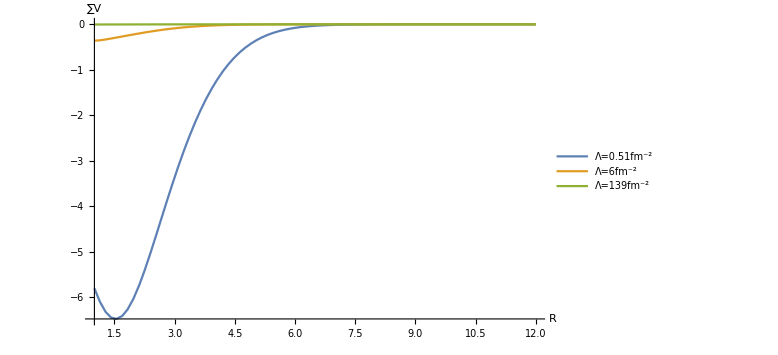

```mathematica
Rmax=12.0;y0=0.015;alpha=0.1;lambda=4;c0=-1;d0=1;

lambdas={0.51,6,139};
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,c0,d0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
```

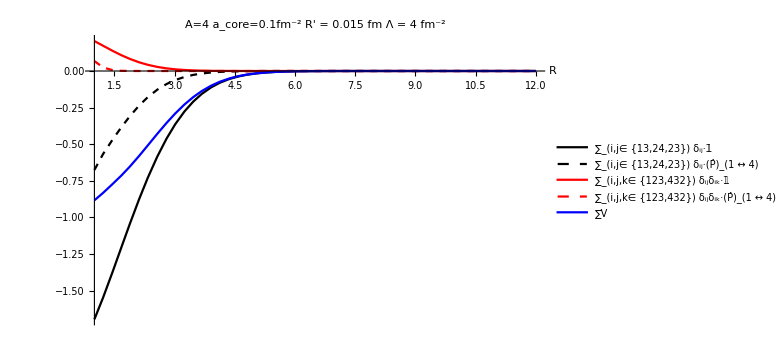
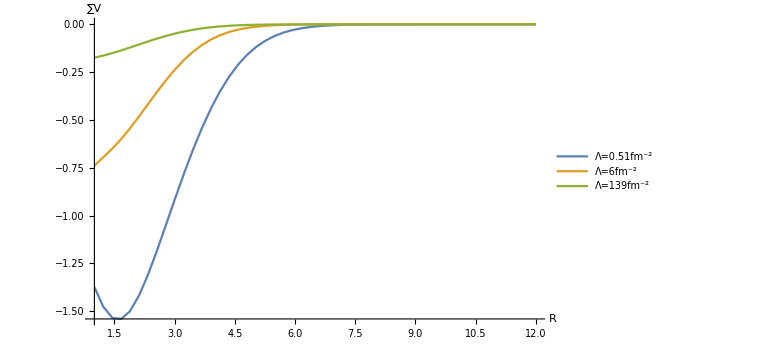
-Graphics- | -Graphics-

```mathematica
Grid[{{
Plot[Evaluate@{Vdi2bdy[r,y0,alpha,c0,lambda],Vex2bdy[r,y0,alpha,c0,lambda],Vdi3bdy[r,y0,alpha,d0,lambda],Vex3bdy[r,y0,alpha,d0,lambda],Vcomplete[r,y0,alpha,lambda,c0,d0]},{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,PlotLabel->"A="<>ToString[A]<>"   a_core="<>ToString[alpha]<>"fm^-2"<>"  R' = "<>ToString[y0]<>" fm    Λ = "<>ToString[lambda]<>" fm^-2",PlotStyle->{{Black},{Black,Dashed},{Red},{Red,Dashed},{Blue,Thick}},AxesLabel->{"R"},PlotLegends->{"∑_(i,j∈
{13,24,23}) δ_ij·𝟙","∑_(i,j∈
{13,24,23}) δ_ij·(P̂)_(1 ↔ 4)","∑_(i,j,k∈
{123,432}) δ_ijδ_ik·𝟙","∑_(i,j,k∈
{123,432}) δ_ijδ_ik·(P̂)_(1 ↔ 4)","∑V"},PlotRange->Full,ImageSize->Large],
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,c0,d0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
}}]
```

## Dimer-Dimer (A_1 B_2) - (A_3 B_4) (scale invariant, 2-body forces only)

V_(ab-ab)=C_0(δ_14+δ_23)  ;  A=𝟙-P_13-P_24+P_13 P_24
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation

```mathematica
RGMequationComponents={};
Do[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={Λ,Λ,0}[[Max[Counts[ijk]]]];
Do[
signpermut=(-1)^(Length[permu]/2);
AppendTo[RGMequationComponents,signpermut genericRGMEQcomponent[x,y,α,α,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]/.λ->WWrange];
,{permu,interFragmentAntisymmetrizer}]
,{ijk,intPart}]
Simplify[1/normierung Total[RGMequationComponents]]
```

2 ((T̂-E)-8 (T̂-E) ⅇ^(-(x^2+y^2) α) α^(3/2)+(4 √2 C_0 (ⅇ^(-(2 x^2 α Λ)/(2 α+Λ))-8 ⅇ^(-α (y^2+(x^2 (2 α+3 Λ))/(2 α+Λ))) α^(3/2)))/(2+Λ/α)^(3/2))

```mathematica
p14={{1,4},{4,1}};
p23={{2,3},{3,2}};p14p23={{1,4},{4,1},{2,3},{3,2}};
normal=iNorm["r","r̃",α]/("(T̂-E)");
iNorm[r_,rp_,omegadimer_]:=genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,{}]
iNormex[r_,rp_,omegadimer_]:=(-genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p14]-genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p23]+genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p14p23])/.{x->r,y->rp,α->omegadimer};
iVdi[r_,rp_,omegadimer_,c0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVex[r_,rp_,omegadimer_,c0_,lambda_]:=(-genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p23]-genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p14p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p14p23]
)/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVcomplete[r_,rp_,omegadimer_,lambda_,c0_]:=iVdi[r,rp,omegadimer,c0,lambda]+iVex[r,rp,omegadimer,c0,lambda];
```

V_(ab-ab)=C_0(δ_13+δ_24)  ;  A=𝟙-P_14-P_23+P_14 P_23
RGM equation:     ⟨ϕ_A ϕ_B|V_(ab-ab)|Â [ϕ_A ϕ_B χ(R)]⟩=0

```mathematica
normal2=2;
```

```mathematica
Clear[Λ];
Print["The factor ",normal normal2," has been divided out to normalize (T̂-E) ECCE the (T̂-E)-∑⇒^?another factor"];
Print["V_(ab - ab)^exchange(r,r') = ",Simplify[1/(normal2 normal) Simplify[iVex["r","r̃",α,Subscript[C, 0],λ]]]];
Print["V_(ab - ab)^direct(r) = ",Simplify[1/(normal2 normal) iVdi["r","r̃",α,Subscript[C, 0],λ]]];
Print["𝟙_(ab - ab)(r) = ",Simplify[1/(normal2 normal) iNorm["r","r̃",α]]];
Print["𝟙_(ab - ab)^ex(r) = ",Simplify[1/(normal2 normal) iNormex["r","r̃",α]]];
```

The factor π^(3/2)/(64 √2 α^3) has been divided out to normalize (T̂-E) ECCE the (T̂-E)-∑⇒^?another factor

V_(ab - ab)^exchange(r,r') = 2 √2 α^3 (-(16 ⅇ^(-α ((r̃)^2+(r^2 (2 α+3 λ))/(2 α+λ))))/(2 α+λ)^(3/2)+(ⅇ^(-(2 r^2 α λ)/(2 α+λ)))/(α (2 α+λ))^(3/2)) C_0

V_(ab - ab)^direct(r) = (2 √2 ⅇ^(-(2 r^2 α λ)/(2 α+λ)) α^3 C_0)/(α (2 α+λ))^(3/2)

𝟙_(ab - ab)(r) = (T̂-E)/2

𝟙_(ab - ab)^ex(r) = (T̂-E) (1/2-8 ⅇ^(-((r̃)^2+r^2) α) α^(3/2))

We consider two limits:
ℵ) The local approximation: ∫dr'Ô(r,r')ϕ(r')=o_1(r)ϕ(r)∫dr'o_2(r') assuming O(r,r')=o_1(r)·o_2(r')
ℶ) The zero-range limit  α/λ→0

(V_(ab-ab))^total(r)=^(1-d)√(π/αλ)C_0(-4 √π e^(-3 αr^2)+e^(-2 αr^2))=^(3-d)C_0/32(π/αλ)^(3/2)(-16 π^(3/2)e^(-3 αr^2)+e^(-2 αr^2))
𝟙_(ab-ab)^local(r)=^(1-d)(T̂-E)1/(4α) √(π/2)(3-8 √π e^(-αr^2))→ -ℏ^2/(2μ)∂_r^2 (1/(4α) √(π/2)(3-8 √π e^(-αr^2)))=^(1-d)-ℏ^2/(2μ)1/(4α) √(π/2)(3 ∂_r^2 +8 √π(4 r^2 α^2+2α)e^(-αr^2))
𝟙_(ab-ab)^local(r)=^(3-d)(T̂-E)π^(3/2)/(128 √2 α^3)(3-32 π^(3/2)e^(-αr^2))→ -ℏ^2/(2μ)∂_r^2 π^(3/2)/(128 √2 α^3)(3-32 π^(3/2)e^(-αr^2))=^(3-d)-ℏ^2/(2μ)π^(3/2)/(128 √2 α^3)(3 ∂_r^2 +32π^(3/2)(4 r^2 α^2+2α)e^(-αr^2))
and finally, the S-wave-projected RGM equation in local form and zero-range approximation for E→0:
 (1-dimensional):  ⟨ϕ_A ϕ_B|𝟙_(ab-ab)^local+(V_(ab-ab))^total|Â [ϕ_A ϕ_B χ(R)]⟩=[-ℏ^2/(2μ)(∂_r^2 +8/3 √π(4 r^2 α^2+2α)e^(-αr^2))+4/3 C_0 √((2α)/λ) (-4 √π e^(-3 αr^2)+e^(-2 αr^2))]χ(r)=0
 (3-dimensional): ⟨ϕ_A ϕ_B|𝟙_(ab-ab)^local+(V_(ab-ab))^total|Â [ϕ_A ϕ_B χ(R)]⟩=[-ℏ^2/(2μ)(∂_r^2 +32/3π^(3/2)(4 r^2 α^2+2α)e^(-αr^2))+8/3 √2(C_0(α/λ))^(3/2) (-8 π^(3/2)e^(-3 αr^2)+e^(-2 αr^2))]χ(r)=0

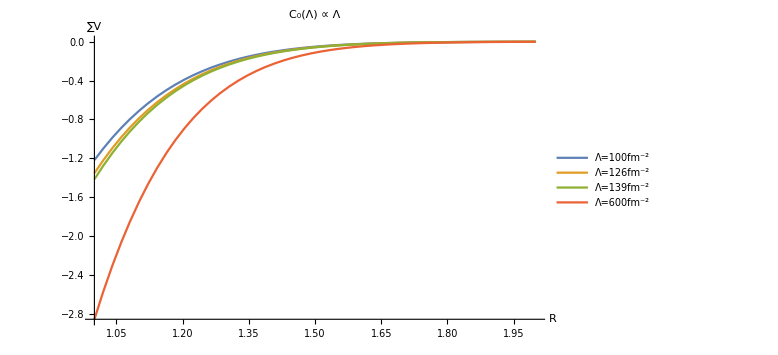

```mathematica
Rmax=2.0;y0=10.0;alpha=1.3;c0=-1;

lambdas={100,126,139,600};
Plot[Evaluate@Table[iVcomplete[r,y0,alpha,lambda,lambda c0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large,PlotLabel->"C_0/(√λ) ∝ Λ"]
```

## Dimer-Dimer (AB)-(CD) (scale variant with 3-body forces, trimer (ABC-D) and tetramer (ABCD) thresholds are assumed to be well separated)

V_(ab-cd)=C_0(δ_13+δ_14+δ_23+δ_24)+D_1(δ_123+δ_124+δ_134+δ_234)  ;  A=𝟙
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation

```mathematica
ints={{1,3,1},{1,4,1},{2,3,2},{2,4,2},{1,2,3},{1,2,4},{1,3,4},{2,3,4}};
Vcomplete[r_,rp_,omegadimer_,lambda_,c0_,d0_]:=Simplify[Total[Table[If[tuple[[1]]==tuple[[3]],
genericRGMEQcomponent[x,y,α,α,c0,Λ,tuple[[1]],tuple[[2]],tuple[[3]],{}],
genericRGMEQcomponent[x,y,α,α,d0,Λ,tuple[[1]],tuple[[2]],tuple[[3]],{}]]
,{tuple,ints}]]]/.{x->r,y->rp,α->omegadimer,Λ->lambda};
```

```mathematica
Clear[Λ];
Simplify[Vcomplete["r","r̃",α,Λ,Subscript[C, 0],Subscript[D, 1]]]
```

1/16 π^(3/2) (ⅇ^(-(2 r^2 α Λ)/(2 α+Λ)) (1/(2 α^2+α Λ))^(3/2) C_0^3+√2 (ⅇ^(-(4 r^2 α Λ)/(2 α+Λ)) (1/(2 α+Λ)^2)^(3/2)+ⅇ^(-(4 r^2 α Λ (α+Λ))/(4 α^2+6 α Λ+Λ^2)) (1/(4 α^2+6 α Λ+Λ^2))^(3/2)) D_1^3)

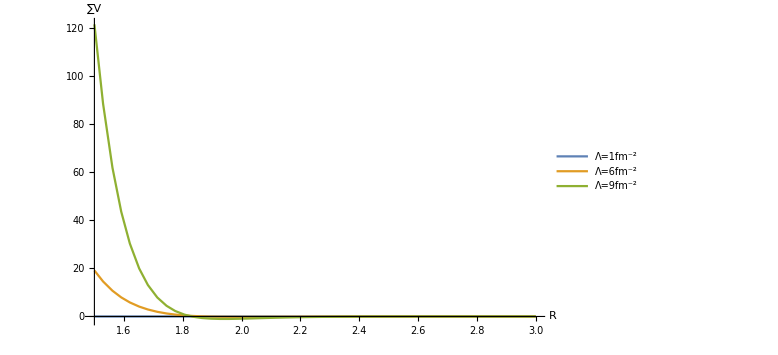

```mathematica
Rmax=3.0;y0=0.0;alpha=1.2;c0=-1;d0=1;

lambdas={1,6,9};
Plot[Evaluate@Table[Vcomplete[r,y0,alpha,lambda,lambda^2 c0,lambda^3 d0],{lambda,lambdas}],{r,1.5,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large]
```

## Trimer-Trimer (ABC)-(ABC) (2- and 3-body forces only)

V_(abc-abc)=C_0(δ_15+δ_16+δ_24+δ_26+δ_34+δ_35)+D_1(δ_126+δ_156+δ_234+δ_246+δ_345)  ;  A=𝟙-P_14-P_25-P_36+P_14 P_25+P_14 P_36+P_25 P_36-P_14 P_25 P_36
RGM equation:     ⟨ϕ_A ϕ_B|(T̂-E+V)|Â [ϕ_A ϕ_B χ(R)]⟩=0
avg. ⟨...⟩ over fragment-internal coordinates;       R: inter-fragment  separation

```mathematica
p14={{1,4},{4,1}};
p23={{2,3},{3,2}};p14p23={{1,4},{4,1},{2,3},{3,2}};
```

```mathematica
normal=iNorm["r","r̃",α]/("(T̂-E)");
iNorm[r_,rp_,omegadimer_]:=genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,{}]
iNormex[r_,rp_,omegadimer_]:=(-genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p14]-genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p23]+genericRGMEQcomponent[x,y,α,α,"(T̂-E)",0,1,3,1,p14p23])/.{x->r,y->rp,α->omegadimer};
iVdi[r_,rp_,omegadimer_,c0_,lambda_]:=(genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,{}]+genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,{}])/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVex[r_,rp_,omegadimer_,c0_,lambda_]:=(-genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p14]-genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p23]-genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,1,3,1,p14p23]+
genericRGMEQcomponent[x,y,α,α,c0,Λ,2,4,2,p14p23]
)/.{x->r,y->rp,α->omegadimer,Λ->lambda};
iVcomplete[r_,rp_,omegadimer_,lambda_,c0_]:=iVdi[r,rp,omegadimer,c0,lambda]+iVex[r,rp,omegadimer,c0,lambda];
```

V_(ab-ab)=C_0(δ_13+δ_24)  ;  A=𝟙-P_14-P_23+P_14 P_23
RGM equation:     ⟨ϕ_A ϕ_B|V_(ab-ab)|Â [ϕ_A ϕ_B χ(R)]⟩=0

```mathematica
normal2=2;
```

```mathematica
Clear[Λ];
Print["The factor ",normal normal2," has been divided out to normalize (T̂-E) ECCE the (T̂-E)-∑⇒^?another factor"];
Print["V_(ab - ab)^exchange(r,r') = ",Simplify[1/(normal2 normal) Simplify[iVex["r","r̃",α,Subscript[C, 0],λ]]]];
Print["V_(ab - ab)^direct(r) = ",Simplify[1/(normal2 normal) iVdi["r","r̃",α,Subscript[C, 0],λ]]];
Print["𝟙_(ab - ab)(r) = ",Simplify[1/(normal2 normal) iNorm["r","r̃",α]]];
Print["𝟙_(ab - ab)^ex(r) = ",Simplify[1/(normal2 normal) iNormex["r","r̃",α]]];
```

The factor π^(3/2)/(64 √2 α^3) has been divided out to normalize (T̂-E) ECCE the (T̂-E)-∑⇒^?another factor

V_(ab - ab)^exchange(r,r') = 2 √2 α^3 (-(16 ⅇ^(-α ((r̃)^2+(r^2 (2 α+3 λ))/(2 α+λ))))/(2 α+λ)^(3/2)+(ⅇ^(-(2 r^2 α λ)/(2 α+λ)))/(α (2 α+λ))^(3/2)) C_0

V_(ab - ab)^direct(r) = (2 √2 ⅇ^(-(2 r^2 α λ)/(2 α+λ)) α^3 C_0)/(α (2 α+λ))^(3/2)

𝟙_(ab - ab)(r) = (T̂-E)/2

𝟙_(ab - ab)^ex(r) = (T̂-E) (1/2-8 ⅇ^(-((r̃)^2+r^2) α) α^(3/2))

We consider two limits:
ℵ) The local approximation: ∫dr'Ô(r,r')ϕ(r')=o_1(r)ϕ(r)∫dr'o_2(r') assuming O(r,r')=o_1(r)·o_2(r')
ℶ) The zero-range limit  α/λ→0

(V_(ab-ab))^total(r)=^(1-d)√(π/αλ)C_0(-4 √π e^(-3 αr^2)+e^(-2 αr^2))=^(3-d)C_0/32(π/αλ)^(3/2)(-16 π^(3/2)e^(-3 αr^2)+e^(-2 αr^2))
𝟙_(ab-ab)^local(r)=^(1-d)(T̂-E)1/(4α) √(π/2)(3-8 √π e^(-αr^2))→ -ℏ^2/(2μ)∂_r^2 (1/(4α) √(π/2)(3-8 √π e^(-αr^2)))=^(1-d)-ℏ^2/(2μ)1/(4α) √(π/2)(3 ∂_r^2 +8 √π(4 r^2 α^2+2α)e^(-αr^2))
𝟙_(ab-ab)^local(r)=^(3-d)(T̂-E)π^(3/2)/(128 √2 α^3)(3-32 π^(3/2)e^(-αr^2))→ -ℏ^2/(2μ)∂_r^2 π^(3/2)/(128 √2 α^3)(3-32 π^(3/2)e^(-αr^2))=^(3-d)-ℏ^2/(2μ)π^(3/2)/(128 √2 α^3)(3 ∂_r^2 +32π^(3/2)(4 r^2 α^2+2α)e^(-αr^2))
and finally, the S-wave-projected RGM equation in local form and zero-range approximation for E→0:
 (1-dimensional):  ⟨ϕ_A ϕ_B|𝟙_(ab-ab)^local+(V_(ab-ab))^total|Â [ϕ_A ϕ_B χ(R)]⟩=[-ℏ^2/(2μ)(∂_r^2 +8/3 √π(4 r^2 α^2+2α)e^(-αr^2))+4/3 C_0 √((2α)/λ) (-4 √π e^(-3 αr^2)+e^(-2 αr^2))]χ(r)=0
 (3-dimensional): ⟨ϕ_A ϕ_B|𝟙_(ab-ab)^local+(V_(ab-ab))^total|Â [ϕ_A ϕ_B χ(R)]⟩=[-ℏ^2/(2μ)(∂_r^2 +32/3π^(3/2)(4 r^2 α^2+2α)e^(-αr^2))+8/3 √2(C_0(α/λ))^(3/2) (-8 π^(3/2)e^(-3 αr^2)+e^(-2 αr^2))]χ(r)=0

```mathematica
Rmax=2.0;y0=10.0;alpha=1.3;c0=-1;

lambdas={100,126,139,600};
Plot[Evaluate@Table[iVcomplete[r,y0,alpha,lambda,lambda c0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->Automatic,MaxRecursion->0,AxesLabel->{"R","∑V"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large,PlotLabel->"C_0/(√λ) ∝ Λ"]
```

-Graphics-